```mathematica
r1 =4.725;
k1=250;
b = .8;
γ= 1/35;
ϕ= .07;
k2 = (565+1350)/2;
μj = .042;
μa=1/140;
α1=.000001;
ρ=(1/(80-35))*(1/100)*.8;
ϵ=.113;
ω=.35;
k3=60000;
μb=1/3;
θj=1/(1111*250*(1-.0027));
θa=0.7/(1111*250*(1-.0027));
θt=0.63/(1111*250*(1-.0027));
σ=2.43175;
```

```mathematica
rd1 = (r1*γ)/(μa(μj +γ))
rd2 = (r1*γ)/((μa+α1)(μj +γ))
bigE = ϵ*μa/γ;
y = ((α1*ρ)/ϕ)*((ϵ/γ)-((b*k2*ρ)/(μa*ϕ*rd1)))(x^2) - (ϵ*((μa+α1)/γ)+((b*k2*ρ)/ϕ)(1-(1/rd2))+(k1+b*k2)*((α1*ρ)/(ϕ*μa*rd1))+1)x + (k1+b*k2)(1-(1/rd2));
```

267.814

267.776

```mathematica
rd1>(ρ*k2*b)/(bigE*ϕ)
rd2>1
ϕ>ρ
```

True

True

True

```mathematica
Solve[y==0]
```

{{x→341.225},{x→3.97549×10^8}}

```mathematica
ϕ/ρ
```

393.75

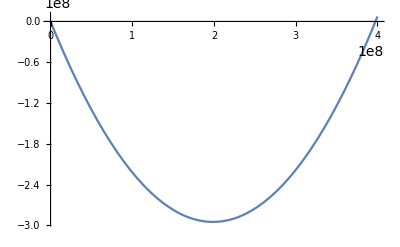

```mathematica
Plot[y,{x, 390,4*^8}]
```

```mathematica
buffelJ = ({{(-r1*ϵ*sa)/(k1+b*t)-(μj+γ), r1*(1-(ϵ*sj+2*sa)/(k1+b*t)), r1*b*sa*((ϵ*sj+sa)/(k1+b*t)^2)}, {γ, -μa - α1*(t/k2), -α1*(sa/k2)}, {0, -ϕ*σ*(t/k2), ϕ*(1-(2*t+σ*sa)/k2)}})
```

{{-0.869715,-9.61892,8.70722},{1/35,-0.00714287,-4.06003×10^-7},{0,-0.00216242,-0.000889357}}

```mathematica
sa = 341.22540
sj = ((μa+α1)/γ)*sa - ((α1*ρ)/(γ*ϕ))*sa^2
t = k2(1-(ρ/ϕ)*sa)
```

341.225

85.3079

127.726

```mathematica
buffelJ//FullSimplify//MatrixForm
```

(-0.869715 | -9.61892 | 8.70722
1/35 | -0.00714287 | -4.06003×10^-7
0 | -0.00216242 | -0.000889357)

```mathematica
Eigenvalues[buffelJ]
```

{-0.437463+0.296608 ⅈ,-0.437463-0.296608 ⅈ,-0.00282049+0. ⅈ}